```mathematica
(*使用Manipulate创建交互式绘图*)
Manipulate[
Module[
{line,circle,point,pointCurve},
(* 绘制数轴 *)
line=Graphics[{
Line[{{0,0},{6Pi,0}}],
Table[Text[ToString[i]<>"π",{i Pi,-0.5}],{i,0,6}]}];
(* 绘制圆周 *)
circle=ParametricPlot[
{Cos[t]+φ,1+Sin[t]},{t,0,2Pi},
PlotStyle->Blue];
(* 绘制动点 *)
point=Graphics[{
PointSize[Large],
Red,
Point[{φ-Sin[φ],1-Cos[φ]}]}];
(* 绘制动点轨迹 *)
pointCurve=ParametricPlot[
{t-Sin[t],1-Cos[t]},{t,0,φ},
PlotStyle->Red
];
Show[line,circle,point,pointCurve,PlotRange->{{-2,6 Pi+2},{-2,3}},ImageSize->Scaled[0.75],Epilog->{Text[Style["φ = "<>ToString[φ/π]<>"π",16,Bold],Scaled[{0.85,0.9}]]}]],
{φ,0.001,6Pi}]
```

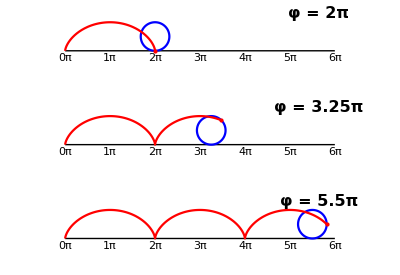

```mathematica
GraphicsColumn[Table[Module[{line,circle,point,pointCurve},
(*设置 n 的值*)
n=nValue;
(*计算 phi*)
φ=n π;
(*绘制数轴*)
line=Graphics[{Line[{{0,0},{6 Pi,0}}],Table[Text[ToString[i]<>"π",{i Pi,-0.5}],{i,0,6}]}];
(*绘制圆周*)
circle=ParametricPlot[{Cos[t]+φ,1+Sin[t]},{t,0,2 Pi},PlotStyle->Blue];
(*绘制动点*)
point=Graphics[{PointSize[Large],Red,Point[{φ-Sin[φ],1-Cos[φ]}]}];
(*绘制动点轨迹*)
pointCurve=ParametricPlot[{t-Sin[t],1-Cos[t]},{t,0,φ},PlotStyle->Red];
Show[line,circle,point,pointCurve,PlotRange->{{-2,6 Pi+2},{-2,3}},ImageSize->Scaled[1.5],Epilog->{Text[Style["φ = "<>ToString[φ/π]<>"π",16,Bold],Scaled[{0.85,0.9}]]}]],
{nValue,{2,3.25,5.5}}]]
```